{{RGBColor[1, Rational[77, 255], Rational[148, 255]],Polygon[…]},{RGBColor[1, 1, 0],Triangle[{{0,0},{0,1/2},{1,0}}]},{RGBColor[0, 0, 1],Thickness[0.01],Circle[{0,0},1,{0,π/2}]},{RGBColor[Rational[2, 5], Rational[194, 255], 1],Opacity[0.5],Disk[{0.59103,0.375079},0.3]}}

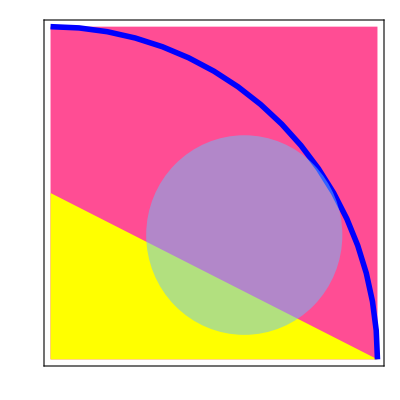
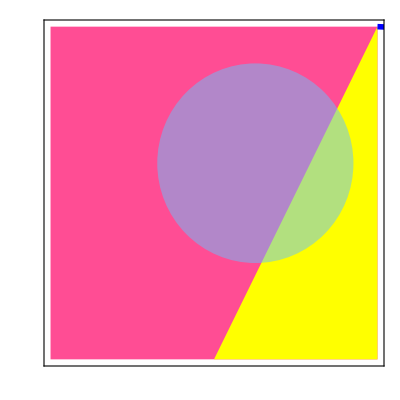
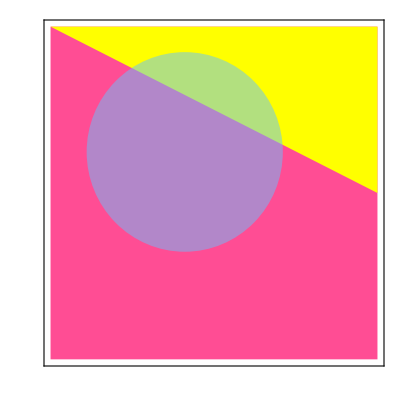
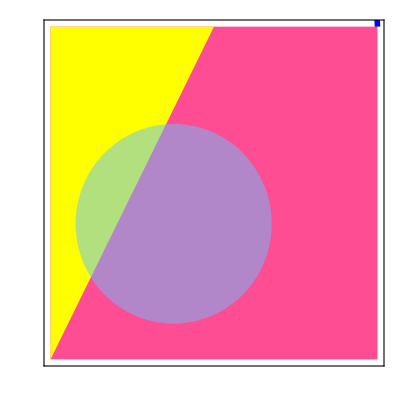
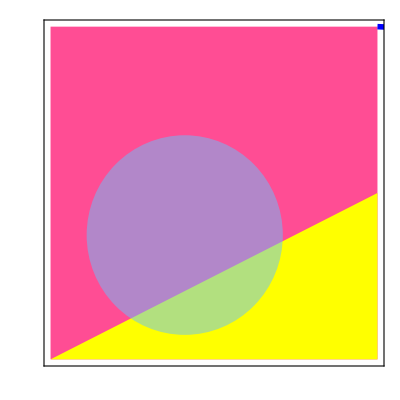
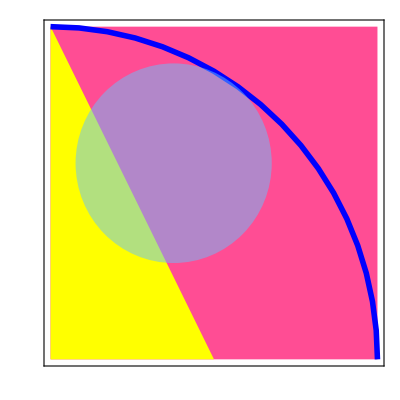
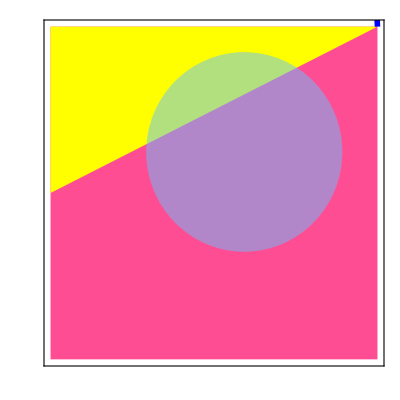
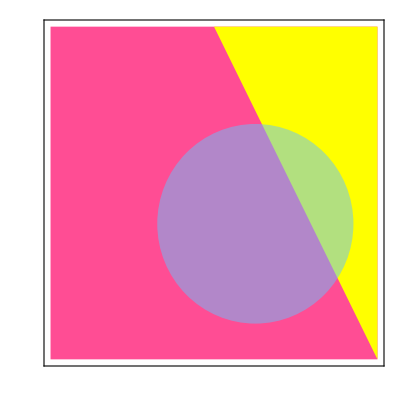
Grid[{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}]

Thread::tdlen: Objects of unequal length in :ff0c\ {InterpretationBox[ButtonBox[
    TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[1, 1, 0], RectangleBox[{0, -1}, {2, 1}]}},AspectRatio->1,DefaultBaseStyle->"ColorSwatchGraphics",Frame->True,FrameStyle->RGBColor[0.6666666666666666, 0.6666666666666666, 0.],FrameTicks->None,ImageSize->Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]}],PlotRangePadding->None],StyleBox[RowBox[{"RGBColor", "[", RowBox[{"1", ",", "1", ",", "0"}], "]"}], NumberMarks -> False]],Appearance->None,BaseStyle->{},BaselinePosition->Baseline,ButtonFunction:>With[{Typeset`box$ = EvaluationBox[]}, If[Not[AbsoluteCurrentValue["Deployed"]], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 1, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]],DefaultBaseStyle->{},Evaluator->Automatic,Method->"Preemptive"],RGBColor[1, 1, 0],Editable->False,Selectable->False], Triangle[{{0, 0}, {0, FractionBox[1, 2]}, {1, 0}}]}\ {InterpretationBox[ButtonBox[
    TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[1, 1, 0], RectangleBox[{0, -1}, {2, 1}]}},AspectRatio->1,DefaultBaseStyle->"ColorSwatchGraphics",Frame->True,FrameStyle->RGBColor[0.6666666666666666, 0.6666666666666666, 0.],FrameTicks->None,ImageSize->Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]}],PlotRangePadding->None],StyleBox[RowBox[{"RGBColor", "[", RowBox[{"1", ",", "1", ",", "0"}], "]"}], NumberMarks -> False]],Appearance->None,BaseStyle->{},BaselinePosition->Baseline,ButtonFunction:>With[{Typeset`box$ = EvaluationBox[]}, If[Not[AbsoluteCurrentValue["Deployed"]], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 1, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]],DefaultBaseStyle->{},Evaluator->Automatic,Method->"Preemptive"],RGBColor[1, 1, 0],Editable->False,Selectable->False], Opacity[0.5`], Disk[{0.5`, 0.4`}, 0.3`]} cannot be combined.

```mathematica
SETTING1by1 = { 
			AspectRatio-> 1,
			PlotRange ->  { {0,1}, {0,1} },

			FrameTicks-> None,
			Frame-> True,
			FrameStyle->Directive[Black,Thickness[0.005]]
                        };

myMotief = {
{RGBColor[255/255,77/255,148/255], Polygon[{{0,0},{0,1},{1,1},{1,0}}]},
{Yellow, Triangle[{{0,0},{0,1/2},{1,0}}]},
{Blue, Thickness[0.01],Circle[ {0,0}, 1, {0, Pi/2} ] },
{RGBColor[102/255,194/255,255/255], Opacity[0.5], Disk[{0.7* Cos[Pi* 0.18],0.7* Sin[Pi * 0.18]}, 0.3]}
}

A = myMotief;

r90 = GeometricTransformation[ A ,  RotationTransform[ Pi/2, {1/2,1/2}]  ];
r180 = GeometricTransformation[ A ,  RotationTransform[ Pi, {1/2,1/2}]  ];
r270  = GeometricTransformation[ A ,  RotationTransform[ 3 * Pi/2, {1/2,1/2}]  ];

a = GeometricTransformation[A, ReflectionTransform[{1,0},{1/2,1/2}]];
b = GeometricTransformation[A, ReflectionTransform[{-1,1},{1/2,1/2}]];
c = GeometricTransformation[A, ReflectionTransform[{0,-1},{1/2,1/2}]];
d = GeometricTransformation[A, ReflectionTransform[{1,1},{1/2,1/2}]];
Grid[{Graphics[A,SETTING1by1]}, 
{Graphics[r90,SETTING1by1]},
{Graphics[r180,SETTING1by1]},
{Graphics[r270,SETTING1by1]},
{Graphics[a,SETTING1by1]},
{Graphics[b,SETTING1by1]},
{Graphics[c,SETTING1by1]},
{Graphics[d,SETTING1by1]}]
```